## Dunaev Viktor, 3 kurs, 6 group, 23 variant

## Pre - Task

```mathematica
fname = NotebookDirectory[]<>"input.txt"
```

C:\6_Cemestr\DS_Laguto\input.txt

```mathematica
stream = OpenRead[fname];
```

```mathematica
information = ReadList[stream,String]
```

{/*|I|*/ 6,/*|U|*/ 12,{1,5},{2,5},{3,1},{3,4},{3,5},{4,1},{4,2},{4,6},{5,4},{6,2},{6,3},{6,5},/*b_1*/ 7,/*b_2*/ 4,/*b_3*/ -1,/*b_4*/ -7,/*b_5*/ -2,/*b_6*/ -1}

```mathematica
numVertex = Read[StringToStream[StringSplit[information⟦1⟧]⟦2⟧],Number]
```

6

```mathematica
MyVertex = Table[i,{i,1,numVertex}]
```

{1,2,3,4,5,6}

```mathematica
numEdges = Read[StringToStream[StringSplit[information⟦2⟧]⟦2⟧],Number]
```

12

```mathematica
MyEdges = Table[
list = StringSplit[information⟦i⟧,{"{","}",","}];
Read[StringToStream[list⟦1⟧],Number]->Read[StringToStream[list⟦2⟧],Number],
{i,3,2+numEdges}
]
```

{1→5,2→5,3→1,3→4,3→5,4→1,4→2,4→6,5→4,6→2,6→3,6→5}

```mathematica
Close[stream]
```

C:\6_Cemestr\DS_Laguto\input.txt

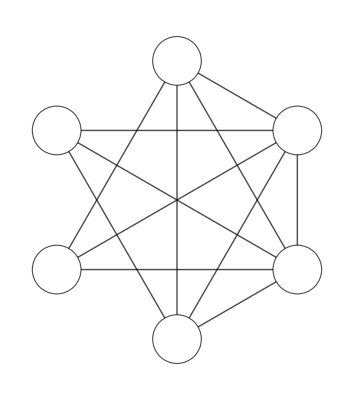

```mathematica
myGraph = Graph[MyVertex,MyEdges,VertexLabels->Placed["Name",Center], GraphLayout->"CircularEmbedding",VertexSize->0.35, VertexStyle->White,EdgeShapeFunction->GraphElementData["Arrow","ArrowSize"->0.035],EdgeStyle->Black,VertexLabelStyle->Large]
```

## Task 1

```mathematica
(* построить покрывающее дерево для индивидуального графа,отобразить его в задании *)
```

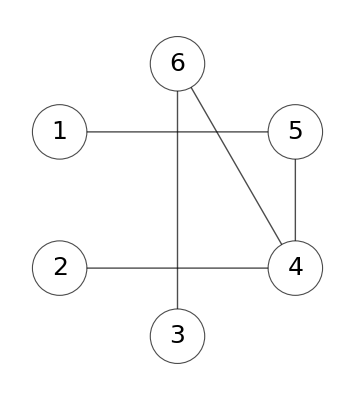

```mathematica
spaningTree = FindSpanningTree[myGraph,VertexSize->Large, VertexStyle->White, VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Black,Italic,25], GraphLayout->{"CircularEmbedding"},EdgeShapeFunction->"Arrow", EdgeStyle->Black]
```

## Task 2

```mathematica
(* выбрать произвольно узел-корень дерева,перейти к корневому дереву:
построить списковые структуры хранения корневого дерева (список узлов,список предков,
список направлений,список глубин узлов,список связи или династического обхода *)
```

```mathematica
startNode = RandomChoice[MyVertex]
```

2

```mathematica
dirs= Table[0,Length[MyVertex]]
```

{0,0,0,0,0,0}

```mathematica
pred = Table[0, Length[MyVertex]]
```

{0,0,0,0,0,0}

```mathematica
depth = Table[0 , Length[MyVertex]]
```

{0,0,0,0,0,0}

```mathematica
dinast = {}
```

{}

```mathematica
tree = {}
```

{}

```mathematica
graphTree = {}
```

{}

```mathematica
DepthFirstScan[UndirectedGraph@myGraph,startNode,{"FrontierEdge"->((edge =#/.(x_<->y_)->(x->y); AppendTo[tree,edge];If[MemberQ[MyEdges,edge],dirs⟦#⟦2⟧⟧=1;AppendTo[graphTree,edge],dirs⟦#⟦2⟧⟧=-1;AppendTo[graphTree,#⟦2⟧->#⟦1⟧]];pred⟦#⟦2⟧⟧=#⟦1⟧;depth⟦#⟦2⟧⟧ = depth⟦#⟦1⟧⟧+1)&),"PrevisitVertex"->((AppendTo[dinast,#])&)}]
```

{5,2,4,2,6,3}

```mathematica
tree
```

{2->4,4->3,3->6,6->5,5->1}

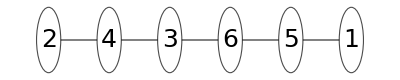

```mathematica
Graph[tree, VertexSize->Large, VertexStyle->White, VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Black,Italic,25], GraphLayout->{"RadialEmbedding"},EdgeShapeFunction->"Arrow", EdgeStyle->Black]
```

## Task 3

```mathematica
(* вывести исходный граф с подсвеченными дугами покрывающего дерева *)
```

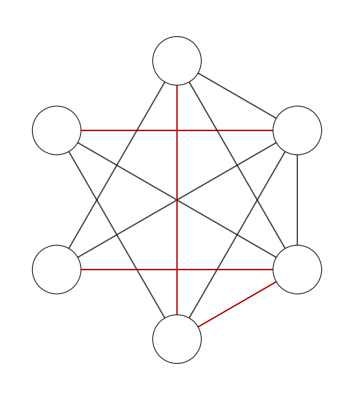

```mathematica
HighlightGraph[myGraph,graphTree]
```

## Task 4

```mathematica
(* списковые структуры вывести в виде таблицы (список связи или династического обхода
 можно не встраивать в таблицу,а вывести отдельным списком) *)
```

```mathematica
TableForm[{MyVertex,pred,depth, dirs},TableHeadings->{{"Вершины:","Предки:","Глубина:", "Направления:"}}]
```

Вершины: | 1 | 2 | 3 | 4 | 5 | 6
Предки: | 5 | 0 | 4 | 2 | 6 | 3
Глубина: | 5 | 0 | 2 | 1 | 4 | 3
Направления: | -1 | 0 | -1 | -1 | -1 | -1

```mathematica
dinast
```

{2,4,3,6,5,1}